```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
```

### Define Functions

```mathematica
BW[w_,wr_,Γ_,δbg_,const_,shift_,shift2_]:=
const((Γ/2)^2/((w-wr)^2+(Γ/2)^2))+ δbg((Γ/2)(w-wr))/((w-wr)^2+(Γ/2)^2)+0 ((4 (w-wr)^2- Γ^2) deltabg^2)/(4 (w-wr)^2+Γ^2)+shift (w-wr)+shift2 ;
BWi[w_,wr_,Γ_,const_]:=const((Γ/2)^2/((w-wr)^2+(Γ/2)^2)) ;

fitnew[input_,output_,len_]:=Module[{temp=Range[1,len],n,maxx,minx,maxy,maxyx,maxyi,maxxy,inter,maxxs,maxxis,maxys,mins,hwhmi,gammas,inputc,bad},
SetSharedVariable[temp];
ParallelDo[n=temp[[ii]];
maxx=Max[input[n][[All,1]]];
minx=Min[input[n][[All,1]]];
maxy=Max[input[n][[All,2]]];
maxyx=input[n][[Position[input[n],Max[input[n][[All,2]]]][[1,1]],1]];
maxyi=Position[input[n][[All,1]],maxyx][[1,1]];
maxxy=input[n][[Position[input[n],Max[input[n][[All,1]]]][[1,1]],2]];
inter=Interpolation[input[n],InterpolationOrder->1];maxxs=Sort[Quiet[DeleteDuplicatesBy[Table[{Round[FindMaxValue[{inter[x],maxyx≤x≤maxx},{x,a}],maxxy],FindArgMax[{inter[x],maxyx≤x≤maxx},{x,a}][[1]]},{a,maxyx,maxx,(maxx-maxyx)/50}],First][[All,2]]]];
bad={};
If[Length[maxxs]>1,Do[If[maxxs[[i+1]]/maxxs[[i]]≤1.001,bad=Append[bad,{i}]],{i,Length[maxxs]-1}]];
maxxs=Delete[maxxs,bad];maxxis=Sort[Table[Position[input[n][[All,1]],Nearest[input[n][[All,1]],maxxs[[i]]][[1]]][[1,1]],{i,Length[maxxs]}]];
bad={};
Do[If[Or[input[n][[maxxis[[i]]-30,2]]>input[n][[maxxis[[i]],2]],input[n][[maxxis[[i]]+30,2]]>input[n][[maxxis[[i]],2]]],bad=Append[bad,{i}]],{i,Length[maxxis]}];maxxs=Delete[maxxs,bad];maxxis=Delete[maxxis,bad];
maxys=Table[input[n][[maxxis[[i]],2]],{i,Length[maxxs]}];
If[Length[maxxs]>1,
mins=Range[Length[maxxs]-1];
Do[mins[[i]]=Position[input[n][[All,2]],Min[input[n][[maxxis[[i]];;maxxis[[i+1]],2]]]][[1,1]],{i,Length[maxxs]-1}];mins=Append[Prepend[mins,maxxis[[1]]-(mins[[1]]-maxxis[[1]])],If[maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]])≤ Length[input[n]],maxxis[[-1]]+(maxxis[[-1]]-mins[[-1]]),Length[input[n]]]];,
hwhmi=Position[input[n],Nearest[input[n][[;;maxyi,2]],maxy/2][[1]]][[1,1]];
mins={maxyi-3(maxyi-hwhmi),If[maxyi+3(maxyi-hwhmi)≤Length[input[n]],maxyi+3(maxyi-hwhmi),Length[input[n]]]};];
If[mins[[1]]<0,mins[[1]]=1];
hwhmi=Range[Length[maxxs]];
Do[hwhmi[[i]]=Position[input[n],Nearest[input[n][[mins[[i]];;maxxis[[i]],2]],inter[maxxs[[i]]]/2][[1]]][[1,1]],{i,Length[maxxs]}];
gammas=Range[Length[hwhmi]];
Do[gammas[[i]]=2(maxxs[[i]]-input[n][[hwhmi[[i]],1]]),{i,Length[hwhmi]}];
inputc=Range[Length[maxxs]];
Do[inputc[[i]]=input[n][[If[i≥2,If[maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])<mins[[i]],mins[[i]],maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])],If[maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]])>0,maxxis[[i]]-3(maxxis[[i]]-hwhmi[[i]]),1]];;If[maxxis[[i]]+3(maxxis[[i]]-hwhmi[[i]])<mins[[i+1]],maxxis[[i]]+3(maxxis[[i]]-hwhmi[[i]]),mins[[i+1]]]]],{i,Length[maxxs]}];
temp[[ii]]=Range[Length[hwhmi]];
Do[temp[[ii,i]]=NonlinearModelFit[inputc[[i]],{BW[w,wr,Γ,δbg,const,shift,shift2],const>0,Γ>0},{{wr,maxxs[[i]]},{Γ,gammas[[i]]},{const,maxys[[i]]},{δbg,0.0},{shift,0.0},{shift2,0.0}},w,MaxIterations->1000],{i,Length[hwhmi]}];,{ii,len}];output=temp;];

store[param_,res_,model_]:=Module[{temp=ToString[res]},res=Range[Length[model]];
Do[res[[i]]=Range[Length[model[[i]]]],{i,Length[model]}];Do[Do[res[[i,ii]]=param/.model[[i,ii]]["BestFitParameters"],{ii,Length[res[[i]]]}],{i,Length[res]}];Export["spectraldata/TBscan/results/"<>temp<>".dat",res];];

storearea[res_,model_]:=Module[{temp=ToString[res]},res=Range[Length[model]];
Do[res[[i]]=Range[Length[model[[i]]]],{i,Length[model]}];Do[Do[res[[i,ii]]=π/2(Γ/.model[[i,ii]]["BestFitParameters"])(const/.model[[i,ii]]["BestFitParameters"]),{ii,Length[res[[i]]]}],{i,Length[res]}];Export["spectraldata/TBscan/results/"<>temp<>".dat",res];];

import[res_]:=res=Import["spectraldata/TBscan/results/"<>ToString[res]<>".dat"];
```

## Critical Temperature 155MeV

```mathematica
πmass=0.14;
```

```mathematica
TBscan=Table[{0.155,i},{i,0.,45 πmass^2,0.01}]
```

{{0.155,0.},{0.155,0.01},{0.155,0.02},{0.155,0.03},{0.155,0.04},{0.155,0.05},{0.155,0.06},{0.155,0.07},{0.155,0.08},{0.155,0.09},{0.155,0.1},{0.155,0.11},{0.155,0.12},{0.155,0.13},{0.155,0.14},{0.155,0.15},{0.155,0.16},{0.155,0.17},{0.155,0.18},{0.155,0.19},{0.155,0.2},{0.155,0.21},{0.155,0.22},{0.155,0.23},{0.155,0.24},{0.155,0.25},{0.155,0.26},{0.155,0.27},{0.155,0.28},{0.155,0.29},{0.155,0.3},{0.155,0.31},{0.155,0.32},{0.155,0.33},{0.155,0.34},{0.155,0.35},{0.155,0.36},{0.155,0.37},{0.155,0.38},{0.155,0.39},{0.155,0.4},{0.155,0.41},{0.155,0.42},{0.155,0.43},{0.155,0.44},{0.155,0.45},{0.155,0.46},{0.155,0.47},{0.155,0.48},{0.155,0.49},{0.155,0.5},{0.155,0.51},{0.155,0.52},{0.155,0.53},{0.155,0.54},{0.155,0.55},{0.155,0.56},{0.155,0.57},{0.155,0.58},{0.155,0.59},{0.155,0.6},{0.155,0.61},{0.155,0.62},{0.155,0.63},{0.155,0.64},{0.155,0.65},{0.155,0.66},{0.155,0.67},{0.155,0.68},{0.155,0.69},{0.155,0.7},{0.155,0.71},{0.155,0.72},{0.155,0.73},{0.155,0.74},{0.155,0.75},{0.155,0.76},{0.155,0.77},{0.155,0.78},{0.155,0.79},{0.155,0.8},{0.155,0.81},{0.155,0.82},{0.155,0.83},{0.155,0.84},{0.155,0.85},{0.155,0.86},{0.155,0.87},{0.155,0.88}}

```mathematica
Do[ccdataTc[n]=Import["spectraldata/TBscan/cc/swccT"<>ToString[Round[1000 TBscan[[n,1]]]]<>"B"<>ToString[Round[1000 TBscan[[n,2]]]]<>"spectra.dat"];,{n,Length[TBscan]}];
Do[ccdataTcu[n]=Import["spectraldata/TBscan/cc/swccT"<>ToString[Round[1000 TBscan[[n,1]]]]<>"B"<>ToString[Round [1000 TBscan[[n,2]]]]<>"uspectra.dat"];,{n,Length[TBscan]}];
Do[ccdataTcl[n]=Import["spectraldata/TBscan/cc/swccT"<>ToString[Round[1000 TBscan[[n,1]]]]<>"B"<>ToString[Round[1000 TBscan[[n,2]]]]<>"lspectra.dat"];,{n,Length[TBscan]}];
```

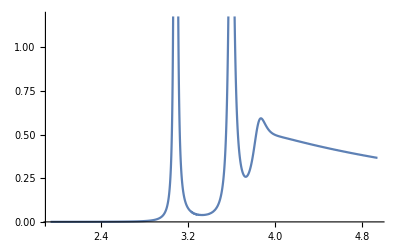

```mathematica
ListPlot[ccdataTcl[2],Joined->True]
```

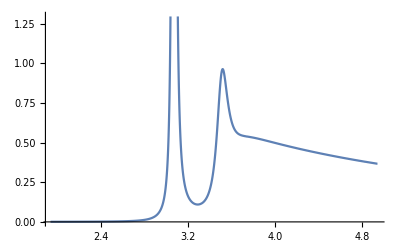

```mathematica
ListPlot[ccdataTc[2],Joined->True]
```

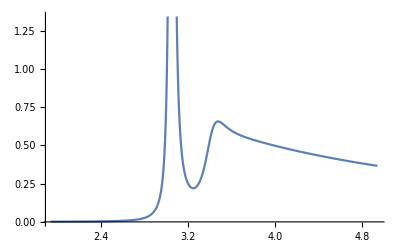

```mathematica
ListPlot[ccdataTcu[2],Joined->True]
```

### Perform Fitting

```mathematica
Clear[ccmodelTc,ccmodelTcl,ccmodelTcu]
fitnew[ccdataTc,ccmodelTc,Length[TBscan]];
fitnew[ccdataTcu,ccmodelTcu,Length[TBscan]];
fitnew[ccdataTcl,ccmodelTcl,Length[TBscan]];
```

```mathematica
Do[If[Length[ccmodelTc[[i]]]>2,ccmodelTc[[i]]=ccmodelTc[[i,;;2]]];,{i,Length[ccmodelTc]}];
Do[If[Length[ccmodelTcu[[i]]]>2,ccmodelTcu[[i]]=ccmodelTcu[[i,;;2]]];,{i,Length[ccmodelTcu]}];
Do[If[Length[ccmodelTcl[[i]]]>2,ccmodelTcl[[i]]=ccmodelTcl[[i,;;2]]];,{i,Length[ccmodelTcl]}];
```

```mathematica
Clear[Tcwrfitcc,Tcgfitcc,Tcareafitcc,Tccfitcc,Tcdfitcc,Tcsfitcc,Tcs2fitcc,Tcwrfitccu,Tcgfitccu,Tcareafitccu,Tccfitccu,Tcdfitccu,Tcsfitccu,Tcs2fitccu,Tcwrfitccl,Tcgfitccl,Tcareafitccl,Tccfitccl,Tcdfitccl,Tcsfitccl,Tcs2fitccl];
store[wr,Tcwrfitcc,ccmodelTc];
store[Γ,Tcgfitcc,ccmodelTc];
store[const,Tccfitcc,ccmodelTc];
store[δbg,Tcdfitcc,ccmodelTc];
store[shift,Tcsfitcc,ccmodelTc];
store[shift2,Tcs2fitcc,ccmodelTc];
storearea[Tcareafitcc,ccmodelTc];
store[wr,Tcwrfitccu,ccmodelTcu];
store[Γ,Tcgfitccu,ccmodelTcu];
store[const,Tccfitccu,ccmodelTcu];
store[δbg,Tcdfitccu,ccmodelTcu];
store[shift,Tcsfitccu,ccmodelTcu];
store[shift2,Tcs2fitccu,ccmodelTcu];
storearea[Tcareafitccu,ccmodelTcu];
store[wr,Tcwrfitccl,ccmodelTcl];
store[Γ,Tcgfitccl,ccmodelTcl];
store[const,Tccfitccl,ccmodelTcl];
store[δbg,Tcdfitccl,ccmodelTcl];
store[shift,Tcsfitccl,ccmodelTcl];
store[shift2,Tcs2fitccl,ccmodelTcl];
storearea[Tcareafitccl,ccmodelTcl];
```

### Import previous results

```mathematica
import[Tcwrfitcc];
import[Tcgfitcc];
import[Tccfitcc];
import[Tcdfitcc];
import[Tcsfitcc];
import[Tcs2fitcc];
import[Tcareafitcc];
import[Tcwrfitccu];
import[Tcgfitccu];
import[Tccfitccu];
import[Tcdfitccu];
import[Tcsfitccu];
import[Tcs2fitccu];
import[Tcareafitccu];
import[Tcwrfitccl];
import[Tcgfitccl];
import[Tccfitccl];
import[Tcdfitccl];
import[Tcsfitccl];
import[Tcs2fitccl];
import[Tcareafitccl];
```

### View results

```mathematica
Manipulate[Show[{ListPlot[ccdataTc[i],Joined->True],Plot[BW[x,Tcwrfitcc[[i,ii]],Tcgfitcc[[i,ii]],Tcdfitcc[[i,ii]],Tccfitcc[[i,ii]],Tcsfitcc[[i,ii]],Tcs2fitcc[[i,ii]]],{x,0.7Tcwrfitcc[[i,ii]],1.3Tcwrfitcc[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,Tcwrfitcc[[i,ii]],Tcgfitcc[[i,ii]],Tccfitcc[[i,ii]]],{x,0.7Tcwrfitcc[[i,ii]],1.3Tcwrfitcc[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}],{i,1,Length[Tcwrfitcc],1},{ii,1,Length[Tcwrfitcc[[1]]],1}]
```

```mathematica
Manipulate[Show[{ListPlot[ccdataTcu[i],Joined->True],Plot[BW[x,Tcwrfitccu[[i,ii]],Tcgfitccu[[i,ii]],Tcdfitccu[[i,ii]],Tccfitccu[[i,ii]],Tcsfitccu[[i,ii]],Tcs2fitccu[[i,ii]]],{x,0.7Tcwrfitccu[[i,ii]],1.3Tcwrfitccu[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,Tcwrfitccu[[i,ii]],Tcgfitccu[[i,ii]],Tccfitccu[[i,ii]]],{x,0.7Tcwrfitccu[[i,ii]],1.3Tcwrfitccu[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}],{i,1,Length[Tcwrfitccu],1},{ii,1,Length[Tcwrfitccu[[1]]],1}]
```

```mathematica
Manipulate[Show[{ListPlot[ccdataTcl[i],Joined->True],Plot[BW[x,Tcwrfitccl[[i,ii]],Tcgfitccl[[i,ii]],Tcdfitccl[[i,ii]],Tccfitccl[[i,ii]],Tcsfitccl[[i,ii]],Tcs2fitccl[[i,ii]]],{x,0.7Tcwrfitccl[[i,ii]],1.3Tcwrfitccl[[i,ii]]},PlotStyle->{Red,Dashed},PlotRange->All],Plot[BWi[x,Tcwrfitccl[[i,ii]],Tcgfitccl[[i,ii]],Tccfitccl[[i,ii]]],{x,0.7Tcwrfitccl[[i,ii]],1.3Tcwrfitccl[[i,ii]]},PlotStyle->{Green,Dashed},PlotRange->All]}],{i,1,Length[Tcwrfitccl],1},{ii,1,Length[Tcwrfitccl[[1]]],1}]
```

### Dilepton ratio

```mathematica
Emfactor=2.356305815440891;
nB[w_,T_]:=1/(Exp[w/T]-1);
```

```mathematica
R0Tc=ConstantArray[0,Length[Tcwrfitcc]];
Do[If[Length[Tcwrfitcc[[ii]]]==2,R0Tc[[ii]]={TBscan[[ii,2]],Emfactor (Tcareafitcc[[ii,2]]nB[Tcwrfitcc[[ii,2]],TBscan[[ii,1]]])/(Tcareafitcc[[ii,1]]nB[Tcwrfitcc[[ii,1]],TBscan[[ii,1]]])}],{ii,Length[R0Tc]}];
R0Tcu=ConstantArray[0,Length[Tcwrfitccu]];
Do[If[Length[Tcwrfitccu[[ii]]]==2,R0Tcu[[ii]]={TBscan[[ii,2]],Emfactor (Tcareafitccu[[ii,2]]nB[Tcwrfitccu[[ii,2]],TBscan[[ii,1]]])/(Tcareafitccu[[ii,1]]nB[Tcwrfitccu[[ii,1]],TBscan[[ii,1]]])}],{ii,Length[R0Tcu]}];
R0Tcl=ConstantArray[0,Length[Tcwrfitccl]];
Do[If[Length[Tcwrfitccl[[ii]]]==2,R0Tcl[[ii]]={TBscan[[ii,2]],Emfactor (Tcareafitccl[[ii,2]]nB[Tcwrfitccl[[ii,2]],TBscan[[ii,1]]])/(Tcareafitccl[[ii,1]]nB[Tcwrfitccl[[ii,1]],TBscan[[ii,1]]])}],{ii,Length[R0Tcl]}];
```

```mathematica
R0Tc=DeleteCases[R0Tc,0];
R0Tcu=DeleteCases[R0Tcu,0];
R0Tcl=DeleteCases[R0Tcl,0];
```

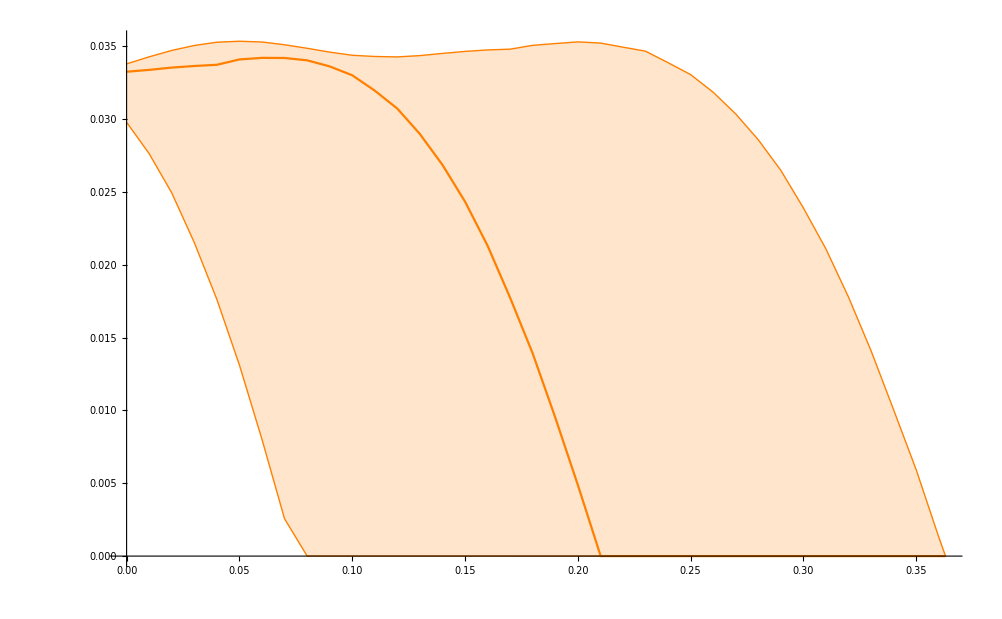

```mathematica
ListPlot[{Append[Append[R0Tc[[;;-44]],{0.21,0.}],{0.363,0.}],Append[R0Tcl[[;;-48]]/.{x_,y_}:>{x,y+2(R0Tc[[1,2]]-R0Tcl[[1,2]])},{0.363,0.}],Append[R0Tcu[[;;-39]],{0.363,0.}]},Joined->True,PlotStyle->{Orange,{Orange,Thin},{Orange,Thin}},Filling->{1->{2},1->{3}}]
```

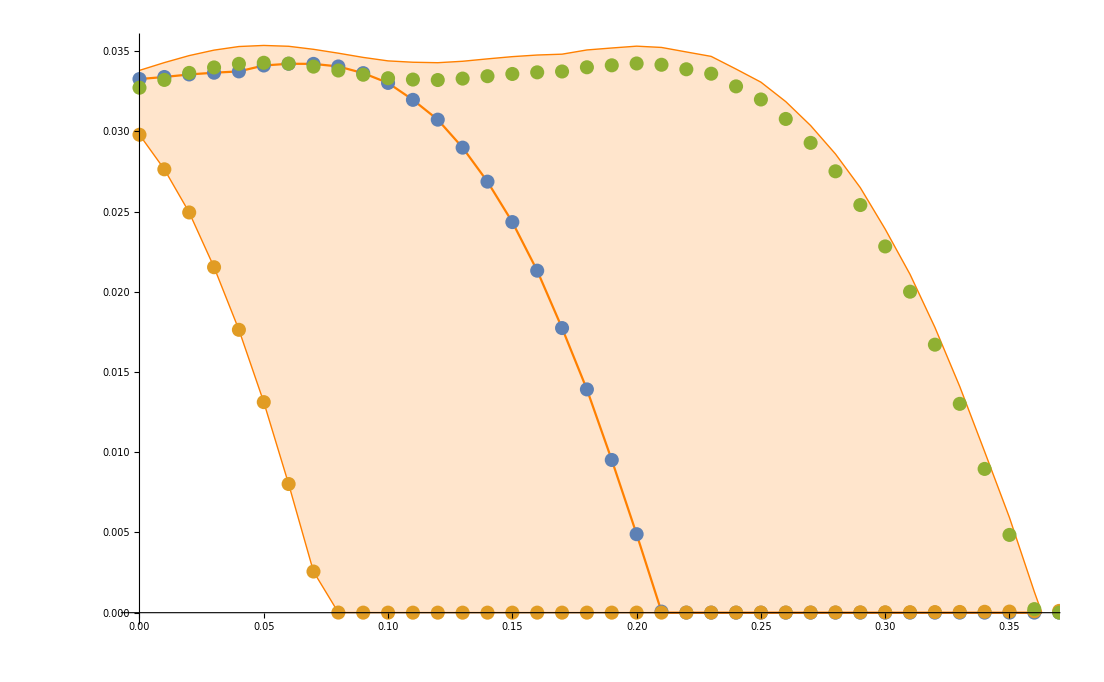

```mathematica
Show[{ListPlot[{Append[Append[R0Tc[[;;-44]],{0.21,0.}],{0.363,0.}],Append[R0Tcl[[;;-48]]/.{x_,y_}:>{x,y+2(R0Tc[[1,2]]-R0Tcl[[1,2]])},{0.363,0.}],Append[R0Tcu[[;;-39]],{0.363,0.}]},Joined->True,PlotStyle->{Orange,{Orange,Thin},{Orange,Thin}},Filling->{1->{2},1->{3}}],ListPlot[{R0Tc,R0Tcu,R0Tcl}]}]
```